```mathematica
Fsol =NDSolve[{F'''[ζ] + 1/2 F[ζ]F''[ζ]==0,F[0]== 0,F'[0]== 0,F''[0]==1},F[ζ],{ζ,0,100}];
```

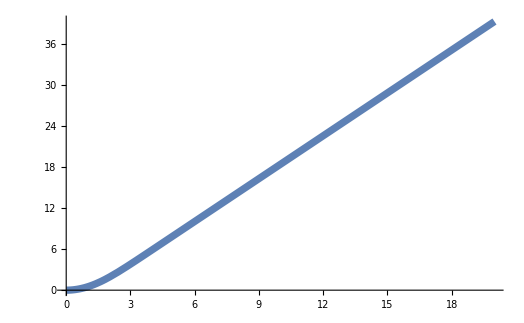

```mathematica
Plot[F[ζ] /. Fsol,{ζ,0,20},PlotStyle -> Thickness[0.01], LabelStyle->Large]
```

```mathematica
CC = D[F[ζ]/. Fsol[[1]],{ζ,1}]/. ζ -> 20
```

2.08541

```mathematica
α = 1/CC^(1/2)
```

0.692475

```mathematica
f[η_]:=α F[ζ]/. Fsol[[1]] /. ζ -> α η
```

```mathematica
f''[0]
```

0.332057

```mathematica
Export["/Users/jbfreund/jbfreund/T/blasius-asm.eps",p,"EPS"];
```

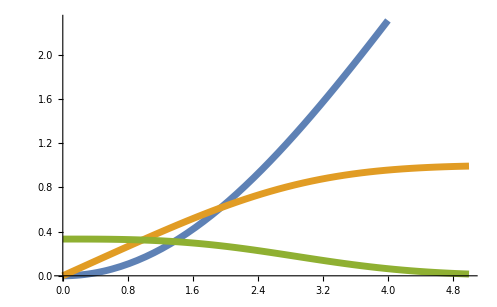

```mathematica
Plot[{f[η],f'[η],f''[η]},{η,0,5},PlotStyle -> Thickness[0.01], LabelStyle->Large]
```

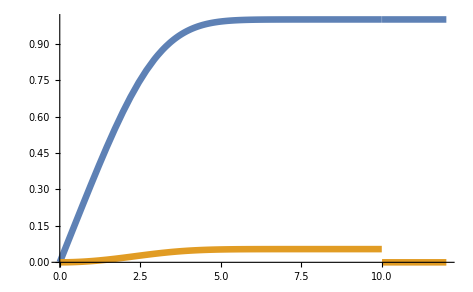

```mathematica
Plot[{f'[η],If[η<10,√(10^-2 1/10)(η f'[η]-f[η]),0]},{η,0,12},PlotStyle -> Thickness[0.01], LabelStyle->Large]
```

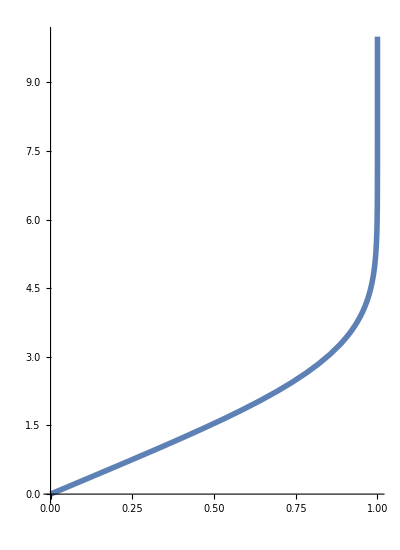

```mathematica
bplt=ParametricPlot[{f'[η],η},{η,0,10},AspectRatio -> GoldenRatio*0.85,PlotStyle ->Thickness[0.01]]
```

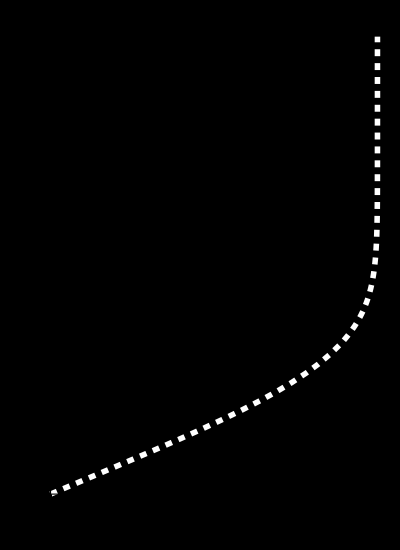

```mathematica
bplt=ParametricPlot[{f'[η],η},{η,0,10},AspectRatio -> GoldenRatio*0.85,PlotStyle -> {White,Dashed,Thickness[0.01]},Background ->  Black]
```

```mathematica
bim = -Graphics-;
```

```mathematica
ImageRotate[bim,1.3π/180]
```

-Graphics-

```mathematica
ImageAdd[ImageRotate[bim,1.3π/180],Show[bplt,PlotRange -> {{.01,1.05},{-.12,7.3}}]]
```

-Graphics-

```mathematica
f[20]-20
```

-1.72079

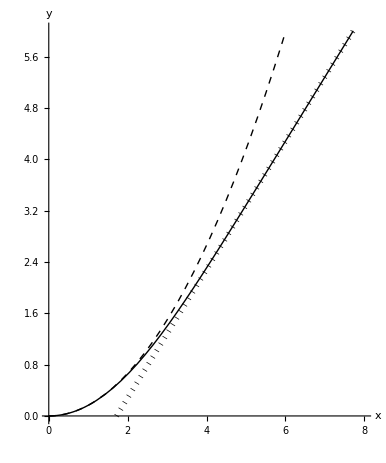

```mathematica
p =Plot[{f[η],0.5 f''[0] η^2,η-(20-f[20])},{η,0,10},PlotStyle -> {{Thick,Black},{Thick,Dashed,Black},{Thickness[0.01],Dotted,Black}},PlotRange -> {{0,8},{0,6}},AspectRatio ->1.2,LabelStyle -> 20,AxesLabel-> {x,y}]
```